# Plotting of energy diagrams and barriers for Nudged Elastic Band calculations

## Simple one-path plot

Inputs are “energypathX” arrays containing positions of image and energies.
For reactants, inter-products and products the positions has to be Integers; fractions are images along reaction coordinates. Then the reactants ... are plotted by longer lines
For different pathways don’t remember to adjust “xtics” so they would fit to your reaction

```mathematica
energypath1=Transpose[{
{0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.16666666666666666,2.3333333333333333,2.5,2.66666666666666662,2.8333333333333334,3,3.25,3.5,3.75,4},
{-578.27064129 ,-578.41861678 ,-578.63156614,-579.32725697 ,-579.22632343 ,
-579.25079259 ,-578.14870473,-580.00534527,-579.52839119 ,
-579.93373698 ,-579.41004016 ,-579.78355202,-579.75633414 ,-580.73183298 ,-580.51964920 ,
-580.29138896,-580.82450731,-580.98703403,-581.00265144}
}]
checkInteger[x_]:=x==Round[x]
Max[energypath1[[All,2]]]-energypath1[[1,2]]
Min[energypath1[[All,2]]]-energypath1[[1,2]]
(*intQ=IntegerQ@Rationalize@#&;*)
```

{{0,-578.271},{0.25,-578.419},{0.5,-578.632},{0.75,-579.327},{1,-579.226},{1.25,-579.251},{1.5,-578.149},{1.75,-580.005},{2,-579.528},{2.1666666666666667,-579.934},{2.33333,-579.41},{2.5,-579.784},{2.6666666666666666,-579.756},{2.83333,-580.732},{3,-580.52},{3.25,-580.291},{3.5,-580.825},{3.75,-580.987},{4,-581.003}}

0.121937

-2.73201

```mathematica
d1={};(*xtics={};*)
For[i=1,i≤Length[energypath1],i++,If[checkInteger[energypath1[[i,1]]],{d1=Append[d1,{energypath1[[i,1]]-0.25,energypath1[[i,2]]-energypath1[[1,2]]}],(*xtics=Append[xtics,{energypath1[[i,1]],"Inter-Product "<>ToString[energypath1[[i,1]]]}],*)d1=Append[d1,{energypath1[[i,1]]+0.25,energypath1[[i,2]]-energypath1[[1,2]]}]},d1=Append[d1,{Floor[energypath1[[i,1]]]+0.25+0.5*(energypath1[[i,1]]-Floor[energypath1[[i,1]]]),energypath1[[i,2]]-energypath1[[1,2]]}]]]
d1=Append[d1,{5.25,-2.7320101500000646}]
(*xtics*)
```

{{-0.25,0.},{0.25,0.},{0.375,-0.147975},{0.5,-0.360925},{0.625,-1.05662},{0.75,-0.955682},{1.25,-0.955682},{1.375,-0.980151},{1.5,0.121937},{1.625,-1.7347},{1.75,-1.25775},{2.25,-1.25775},{2.33333,-1.6631},{2.41667,-1.1394},{2.5,-1.51291},{2.58333,-1.48569},{2.66667,-2.46119},{2.75,-2.24901},{3.25,-2.24901},{3.375,-2.02075},{3.5,-2.55387},{3.625,-2.71639},{3.75,-2.73201},{4.25,-2.73201},{5.25,-2.73201}}

```mathematica
xtics={{0,"Reactant"},{1,"Interproduct 1"},{2,"Interproduct 2"},{3,"Interproduct 3"},{4,"Interproduct 4"},{5,"Product"}};
```

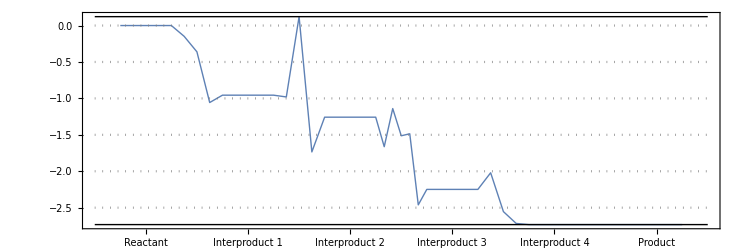

```mathematica
ListLinePlot[{d1,{{-0.5,0.12193655999999464},{5.5,0.12193655999999464}},{{-0.5,-2.7320101500000646},{5.5,-2.7320101500000646}},{{-0.5,0.0},{5.5,0.0}},{{-0.5,-1.0},{5.5,-1.0}},{{-0.5,-2.0},{5.5,-2.0}},{{-0.5,-2.5},{5.5,-2.5}},{{-0.5,-1.5},{5.5,-1.5}},{{-0.5,-0.5},{5.5,-0.5}}},PlotRange->{{-0.5,5.5},Automatic},PlotStyle->{Directive[Thick],Directive[Thin,Black],Directive[Thin,Black],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted]},Axes->False,Frame->True,FrameTicks->{xtics,Automatic},FrameStyle->Directive[Black,Thick,16],ImageSize->750,AspectRatio->1/3]
```

## Multiple-path plot

```mathematica
energypath1=Transpose[{
{0,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.16666666666666666,3.3333333333333333,3.5,3.66666666666666662,3.8333333333333334,4,4.25,4.5,4.75,5},
{-578.27064129 ,
-578.27064129 ,-578.41861678 ,-578.63156614,-579.32725697 ,-579.22632343 ,
-579.25079259 ,-578.14870473,-580.00534527,-579.52839119 ,
-579.93373698 ,-579.41004016 ,-579.78355202,-579.75633414 ,-580.73183298 ,-580.51964920 ,
-580.29138896,-580.82450731,-580.98703403,-581.00265144}
}]
l=Length[energypath1]
d1={};(*xtics={};*)
For[i=1,i≤Length[energypath1],i++,If[checkInteger[energypath1[[i,1]]],{d1=Append[d1,{energypath1[[i,1]]-0.25,energypath1[[i,2]]-energypath1[[l,2]]}],d1=Append[d1,{energypath1[[i,1]]+0.25,energypath1[[i,2]]-energypath1[[l,2]]}]},d1=Append[d1,{Floor[energypath1[[i,1]]]+0.25+0.5*(energypath1[[i,1]]-Floor[energypath1[[i,1]]]),energypath1[[i,2]]-energypath1[[l,2]]}]]]

energypath2=Transpose[{
{2,2.16666666666666666,2.3333333333333333,2.5,2.66666666666666662,2.8333333333333334,3,3.25,3.5,3.75,4},
{-579.22632343 ,
-579.56800765,-579.61112620,-579.28311595,-579.81096912,-579.95073609 ,-579.53477466,
-579.92532073,-579.50211690,-580.49578162,-580.51964920}
}]
d2={};(*xtics={};*)
For[i=1,i≤Length[energypath2],i++,If[checkInteger[energypath2[[i,1]]],{d2=Append[d2,{energypath2[[i,1]]-0.25,energypath2[[i,2]]-energypath1[[l,2]]}],d2=Append[d2,{energypath2[[i,1]]+0.25,energypath2[[i,2]]-energypath1[[l,2]]}]},d2=Append[d2,{Floor[energypath2[[i,1]]]+0.25+0.5*(energypath2[[i,1]]-Floor[energypath2[[i,1]]]),energypath2[[i,2]]-energypath1[[l,2]]}]]]
```

{{0,-578.271},{1,-578.271},{1.25,-578.419},{1.5,-578.632},{1.75,-579.327},{2,-579.226},{2.25,-579.251},{2.5,-578.149},{2.75,-580.005},{3,-579.528},{3.1666666666666667,-579.934},{3.33333,-579.41},{3.5,-579.784},{3.6666666666666666,-579.756},{3.83333,-580.732},{4,-580.52},{4.25,-580.291},{4.5,-580.825},{4.75,-580.987},{5,-581.003}}

20

{{2,-579.226},{2.1666666666666667,-579.568},{2.33333,-579.611},{2.5,-579.283},{2.6666666666666666,-579.811},{2.83333,-579.951},{3,-579.535},{3.25,-579.925},{3.5,-579.502},{3.75,-580.496},{4,-580.52}}

```mathematica
energypath3=Transpose[{
{0,0.25,0.5,0.75,1,1.142857,1.285714,1.428571,1.571429,1.714286,1.857143,2},
{-577.94851103 ,-577.96634417,-577.70501248,-578.61121291,-578.52974538,
(*-287.38071422-291.14903116,*)-287.41402088-291.14903116,-287.55249779-291.14903116,-287.73218272-291.14903116,-287.80949765-291.14903116,-287.74328843-291.14903116,-287.95254043-291.14903116,-579.22632343}
}]
d3={};(*xtics={};*)
For[i=1,i≤Length[energypath3],i++,If[checkInteger[energypath3[[i,1]]],{d3=Append[d3,{energypath3[[i,1]]-0.25,energypath3[[i,2]]-energypath1[[l,2]]}],d3=Append[d3,{energypath3[[i,1]]+0.25,energypath3[[i,2]]-energypath1[[l,2]]}]},d3=Append[d3,{Floor[energypath3[[i,1]]]+0.25+0.5*(energypath3[[i,1]]-Floor[energypath3[[i,1]]]),energypath3[[i,2]]-energypath1[[l,2]]}]]]

energypath4=Transpose[{
{1,1.2,1.4,1.6,1.8,2,2.25,2.5,2.75,3},
{-578.52974538,
-577.96634417-0.58123435,-577.70501248-0.58123435,-578.61121291-0.58123435,-578.52974538-0.58123435,
-579.64681687,
-580.00269695,-580.01122899,-580.12115412 ,-579.53477466
}
}]
d4={};(*xtics={};*)
For[i=1,i≤Length[energypath4],i++,If[checkInteger[energypath4[[i,1]]],{d4=Append[d4,{energypath4[[i,1]]-0.25,energypath4[[i,2]]-energypath1[[l,2]]}],d4=Append[d4,{energypath4[[i,1]]+0.25,energypath4[[i,2]]-energypath1[[l,2]]}]},d4=Append[d4,{Floor[energypath4[[i,1]]]+0.25+0.5*(energypath4[[i,1]]-Floor[energypath4[[i,1]]]),energypath4[[i,2]]-energypath1[[l,2]]}]]]
```

{{0,-577.949},{0.25,-577.966},{0.5,-577.705},{0.75,-578.611},{1,-578.53},{1.14286,-578.563},{1.28571,-578.702},{1.42857,-578.881},{1.57143,-578.959},{1.71429,-578.892},{1.85714,-579.102},{2,-579.226}}

{{1,-578.53},{1.2,-578.548},{1.4,-578.286},{1.6,-579.192},{1.8,-579.111},{2,-579.647},{2.25,-580.003},{2.5,-580.011},{2.75,-580.121},{3,-579.535}}

```mathematica
d2=Delete[Delete[d2,Length[d2]],1];d3=Delete[d3,Length[d3]];d4=Delete[Delete[d4,Length[d4]],1];
m1=Max[d1[[All,2]]]
m3=Max[d3[[All,2]]]
```

2.85395

3.29764

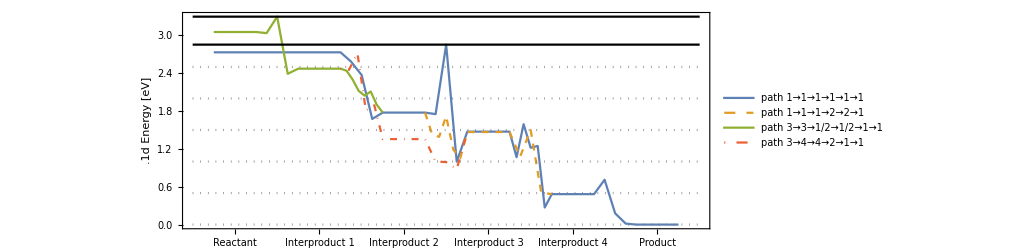

```mathematica
ListLinePlot[{d1,d2,d3,d4,{{-0.5,m1},{5.5,m1}},{{-0.5,m3},{5.5,m3}},{{-0.5,0.0},{5.5,0.0}},{{-0.5,1.0},{5.5,1.0}},{{-0.5,2.0},{5.5,2.0}},{{-0.5,2.5},{5.5,2.5}},{{-0.5,1.5},{5.5,1.5}},{{-0.5,0.5},{5.5,0.5}}},PlotRange->{{-0.5,5.5},Automatic},PlotStyle->{Directive[Thick],Directive[Thick,Dashed],Directive[Thick],Directive[DotDashed],Directive[Thin,Black],Directive[Thin,Black],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted]},Axes->False,Frame->True,FrameTicks->{xtics,Automatic},FrameStyle->Directive[Black,Thick,16],ImageSize->750,FrameLabel->"Energy [eV]".1d,AspectRatio->1/3,PlotLegends->LineLegend[{"path 1→1→1→1→1→1","path 1→1→1→2→2→1","path 3→3→1/2→1/2→1→1","path 3→4→4→2→1→1"}]]
```

```mathematica
Export["./neco.png",-Graphics-]
```

./neco.png

## Simple one-path plot: 28-reaction 3x3 k, single-point

00   energy without entropy= -294.40401247 energy(sigma->0) = -294.58424955
01   energy without entropy= -294.31663981 energy(sigma->0) = -294.49568595
02   energy without entropy= -293.61462810 energy(sigma->0) = -293.79078418
03   energy without entropy= -293.02731503 energy(sigma->0) = -293.22908009
04   energy without entropy= -293.36142233 energy(sigma->0) = -293.53699686
05   energy without entropy= -292.90418285 energy(sigma->0) = -293.10737380

```mathematica
energypath1=Transpose[{
{0,0.2,0.4,0.6,0.8,1},
{-294.40401247 ,-294.31663981 ,-293.61462810 ,-293.02731503 ,-293.36142233 ,-292.90418285}
}]
checkInteger[x_]:=x==Round[x]
Max[energypath1[[All,2]]]-energypath1[[1,2]]
Min[energypath1[[All,2]]]-energypath1[[1,2]]
(*intQ=IntegerQ@Rationalize@#&;*)
```

{{0,-294.404},{0.2,-294.317},{0.4,-293.615},{0.6,-293.027},{0.8,-293.361},{1,-292.904}}

1.49983

0.

```mathematica
d1={};(*xtics={};*)
For[i=1,i≤Length[energypath1],i++,If[checkInteger[energypath1[[i,1]]],{d1=Append[d1,{energypath1[[i,1]]-0.25,energypath1[[i,2]]-energypath1[[1,2]]}],(*xtics=Append[xtics,{energypath1[[i,1]],"Inter-Product "<>ToString[energypath1[[i,1]]]}],*)d1=Append[d1,{energypath1[[i,1]]+0.25,energypath1[[i,2]]-energypath1[[1,2]]}]},d1=Append[d1,{Floor[energypath1[[i,1]]]+0.25+0.5*(energypath1[[i,1]]-Floor[energypath1[[i,1]]]),energypath1[[i,2]]-energypath1[[1,2]]}]]]
(*xtics*)
```

```mathematica
xtics={{0,"Reactant"},{0.5, "images in between"},{1,"Product"}};
```

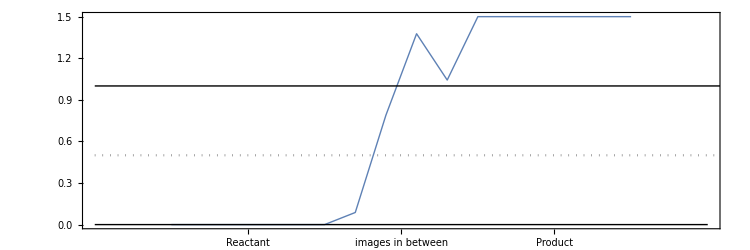

```mathematica
ListLinePlot[{d1,{{-0.5,0.0},{1.5,0.0}},{{-0.5,1.0},{5.5,1.0}},{{-0.5,0.5},{5.5,0.5}}},PlotRange->{{-0.5,1.5},Automatic},PlotStyle->{Directive[Thick],Directive[Thin,Black],Directive[Thin,Black],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted]},Axes->False,Frame->True,FrameTicks->{xtics,Automatic},FrameStyle->Directive[Black,Thick,16],ImageSize->750,AspectRatio->1/3]
```

```mathematica
d1
```

{{-0.25,0.},{0.25,0.},{0.35,0.0873727},{0.45,0.789384},{0.55,1.3767},{0.65,1.04259},{0.75,1.49983},{1.25,1.49983}}

## Simple one-path plot: 29-reaction 3x3 k, single-point

X2   energy without entropy= -294.30633695 energy(sigma->0) = -294.48678058
X1   energy without entropy= -294.36014377 energy(sigma->0) = -294.53986857
00   energy without entropy= -294.41108700 energy(sigma->0) = -294.59144304
01   energy without entropy= -294.43812757 energy(sigma->0) = -294.61846817
02   energy without entropy= -293.59363077 energy(sigma->0) = -293.77343619
03   energy without entropy= -293.63145714 energy(sigma->0) = -293.81053442
04   energy without entropy= -293.14989759 energy(sigma->0) = -293.35043179
05   energy without entropy= -293.08659291 energy(sigma->0) = -293.28783226
06   energy without entropy= -293.51981986 energy(sigma->0) = -293.69565234

```mathematica
energypath1=Transpose[{
{0,0.125,0.25, 0.375, 0.5,0.625, 0.75,0.875,1},
{-294.30633695,-294.36014377 ,-294.41108700 ,-294.43812757 ,-293.59363077 ,-293.63145714, -293.14989759, -293.08659291, -293.51981986}
}]
checkInteger[x_]:=x==Round[x]
Max[energypath1[[All,2]]]-energypath1[[1,2]]
Min[energypath1[[All,2]]]-energypath1[[1,2]]
(*intQ=IntegerQ@Rationalize@#&;*)
```

{{0,-294.306},{0.125,-294.36},{0.25,-294.411},{0.375,-294.438},{0.5,-293.594},{0.625,-293.631},{0.75,-293.15},{0.875,-293.087},{1,-293.52}}

1.21974

-0.131791

```mathematica
d2={};(*xtics={};*)
For[i=1,i≤Length[energypath1],i++,If[checkInteger[energypath1[[i,1]]],{d2=Append[d2,{energypath1[[i,1]]-0.25,energypath1[[i,2]]-energypath1[[1,2]]}],(*xtics=Append[xtics,{energypath1[[i,1]],"Inter-Product "<>ToString[energypath1[[i,1]]]}],*)d2=Append[d2,{energypath1[[i,1]]+0.25,energypath1[[i,2]]-energypath1[[1,2]]}]},d2=Append[d2,{Floor[energypath1[[i,1]]]+0.25+0.5*(energypath1[[i,1]]-Floor[energypath1[[i,1]]]),energypath1[[i,2]]-energypath1[[1,2]]}]]]
(*xtics*)
```

```mathematica
xtics={{0,"Reactant"},{0.5, "images in between"},{1,"Product"}};
```

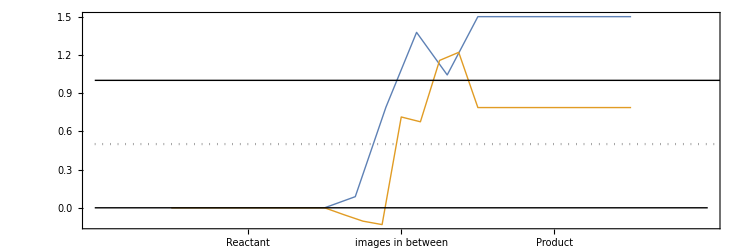

```mathematica
ListLinePlot[{d1,d2,{{-0.5,0.0},{1.5,0.0}},{{-0.5,1.0},{5.5,1.0}},{{-0.5,0.5},{5.5,0.5}}},PlotRange->{{-0.5,1.5},Automatic},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thin,Black],Directive[Thin,Black],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted],Directive[Gray,Dotted]},Axes->False,Frame->True,FrameTicks->{xtics,Automatic},FrameStyle->Directive[Black,Thick,16],ImageSize->750,AspectRatio->1/3]
```

```mathematica
d2
```

{{-0.25,0.},{0.25,0.},{0.3125,-0.0538068},{0.375,-0.10475},{0.4375,-0.131791},{0.5,0.712706},{0.5625,0.67488},{0.625,1.15644},{0.6875,1.21974},{0.75,0.786517},{1.25,0.786517}}